```mathematica
f[x_] := a x^2 + b x +c
```

```mathematica
f[z]
```

c+b z+a z^2

```mathematica
f["pippo"]
```

pippo^2 a+pippo b+c

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
??D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

Attributes[D]={Protected,ReadProtected}
 
Options[D]:={NonConstants→{}}

```mathematica
D[x^3,{x,2}]
```

6 x

```mathematica
D[x^3,{y,4}]
```

0

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^(3/2),x]
```

(3 √x)/2

```mathematica
Dt[x^n,y]
```

x^n ((n Dt[x,y])/x+Dt[n,y] Log[x])

```mathematica
D[f[x],x]
```

b+2 a x

```mathematica
D[g[x],x]
```

g'[x]

```mathematica
D[Sin[Sqrt[x]],{x,2}]
```

-Cos[√x]/(4 x^(3/2))-Sin[√x]/(4 x)

```mathematica
FullForm[g'[x]]
```

Derivative[1][g][x]

```mathematica
D[g[x,y],y]
```

g^(0,1)[x,y]

```mathematica
FullForm[%]
```

Derivative[0,1][g][x,y]

```mathematica
Integrate[g[x],x]
```

∫g[x]ⅆx

```mathematica
Integrate[g'[x],x]
```

g[x]

```mathematica
Series[ g[x], {x,x0,4}]
```

g[x0]+g'[x0] (x-x0)+1/2 g''[x0] (x-x0)^2+1/6 g^(3)[x0] (x-x0)^3+1/24 g^(4)[x0] (x-x0)^4+O[x-x0]^5

```mathematica
%/.(x->1)
```

SeriesData::ssdn: Attempt to evaluate a series at the number 1. Returning Indeterminate.

```mathematica
Indeterminate

Normal[Series[g[x], {x,x0,4}]]
```

Indeterminate

g[x0]+(x-x0) g'[x0]+1/2 (x-x0)^2 g''[x0]+1/6 (x-x0)^3 g^(3)[x0]+1/24 (x-x0)^4 g^(4)[x0]

```mathematica
%/.(x->1)
```

g[x0]+(1-x0) g'[x0]+1/2 (1-x0)^2 g''[x0]+1/6 (1-x0)^3 g^(3)[x0]+1/24 (1-x0)^4 g^(4)[x0]

```mathematica
Normal[Series[Sin[x],{x,0,9}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

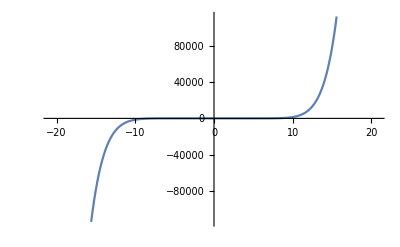

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-20.784609690826528,20.784609690826528}]
```

```mathematica
(* Con quanti termini è necessario sviluppare Log[1+x] nell'intorno di x=0,in modo da valutare Log[0.1] con una accuratezza dello 0.01 percento?*)
```

```mathematica
Log[0.1]
```

-2.30259

```mathematica
Do[ Print[i],{i,1,10}]
```

1

2

3

4

5

6

7

8

9

10

```mathematica
??If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

Attributes[If]={HoldRest,Protected}

```mathematica
??Abs
```

Abs[z] gives the absolute value of the real or complex number z.

Attributes[Abs]={Listable,NumericFunction,Protected,ReadProtected}

```mathematica
??While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

Attributes[While]={HoldAll,Protected}

```mathematica
??While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

Attributes[While]={HoldAll,Protected}

```mathematica
esatto=Log[0.1];
h[n_]=Normal[Series[Log[1+t],{t,0,n}]];
i=0;
While[
  ((Abs[approx/esatto - 1]) <(0.01/100)) ,
approx = h[i]/. (x-> (-0.9));
i=i+1;
     ];

Print["Servono " , i , " termini"];
```

Series::serlim: Series order specification n is not a machine-sized integer.

```mathematica
f[k_]:=Normal[Series[Log[1+x],{x,0,k}]];
esatto=Log[0.1];
Do[
approx = f[i] /.( x-> -0.9);
diff=Abs[approx/esatto-1];
If [diff<0.0001,
  Print["Servono " ,i ," termini"];
  Break[]
]
,
	{i,1,100}
];
```

Servono 61 termini

```mathematica
Integrate[x^(a-1) (1-x)^(b-1),{x,0,1}]
```

ConditionalExpression[(Gamma[a] Gamma[b])/Gamma[a+b],Re[a]>0&&Re[b]>0]

```mathematica
f[a_,b_]:=Integrate[x^(a-1) (1-x)^(b-1),{x,0,1}]
```

```mathematica
f[-2,4]
```

Integrate::idiv: Integral of -1+1/x^3-3/x^2+3/x does not converge on {0,1}.

∫_0^1 (1-x)^3/x^3 ⅆx

```mathematica
sviluppo1=Normal[Series[ Gamma[x],{x,0,5} ]]
```

-EulerGamma+1/x+1/12 (6 EulerGamma^2+π^2) x+1/6 x^2 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+1/24 x^3 (EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1])+1/1440 x^4 (-12 EulerGamma^5-20 EulerGamma^3 π^2-9 EulerGamma π^4+120 EulerGamma^2 PolyGamma[2,1]+20 π^2 PolyGamma[2,1]+12 PolyGamma[4,1])+1/120960 x^5 (168 EulerGamma^6+420 EulerGamma^4 π^2+378 EulerGamma^2 π^4+61 π^6-3360 EulerGamma^3 PolyGamma[2,1]-1680 EulerGamma π^2 PolyGamma[2,1]+1680 PolyGamma[2,1]^2-1008 EulerGamma PolyGamma[4,1])

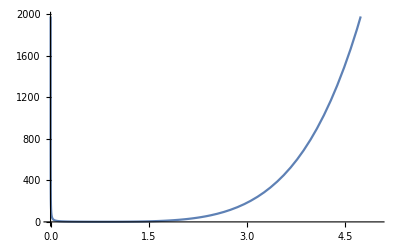

```mathematica
Plot[ sviluppo1 , {x,0,5} ]
```

```mathematica
??Plot*
```

```mathematica
Plot3D[ Sin [x^2 + y^2] , {x,-3,3} , {y,-3,3} , PlotPoints ->100]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x^2+y^2],{x,-3,3},{y,-3,3},PlotStyle->RGBColor[0.89,0.,0.14],PlotPoints->100]
```

-Graphics3D-

```mathematica
??Gamma
```

Gamma[z] is the Euler gamma function Γ(z). 
Gamma[a,z] is the incomplete gamma function Γ(a,z). 
Gamma[a,z_0,z_1] is the generalized incomplete gamma function Γ(a,z_0)-Γ(a,z_1).

Attributes[Gamma]={Listable,NumericFunction,Protected,ReadProtected}

```mathematica
z=x+I y
Plot3D[ Re[Gamma[z]] + Im[ Gamma[z]],{x,-10,10} , {y, -10,10} ]
```

x+ⅈ y

-Graphics3D-

```mathematica
Plot3D[ Re[Gamma[x+ I y]],{x,-3,3},{y, -3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Im[Gamma[x+ I y]] , {x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Integrate[ Sin[x] , x]
```

-Cos[x]

```mathematica
Integrate[1/(1+x^2),x]
```

ArcTan[x]

```mathematica
Integrate[1/(1+x^2),{x,0,+Infinity}]
```

π/2

```mathematica
Integrate[1/(1+x^2),{x,-Infinity,+Infinity}]
```

π

```mathematica
Integrate[1/(1+x^2),{x,+Infinity,0}]
```

-π/2

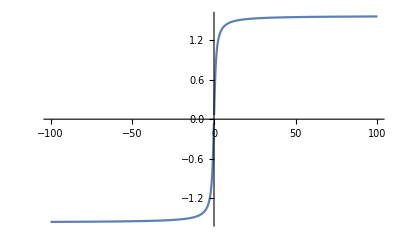

```mathematica
Plot[ArcTan[x],{x,-100,100}]
```

```mathematica
Integrate[3 x^2 , {x,1,4} ]
```

63

```mathematica
Integrate[3 x^2,x]
```

x^3

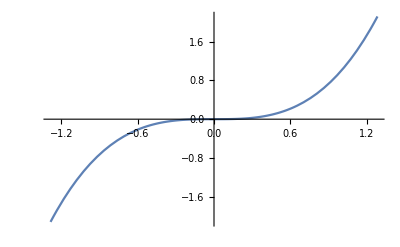

```mathematica
Plot[x^3,{x,-1.2851194708927707,1.2851194708927707}]
```

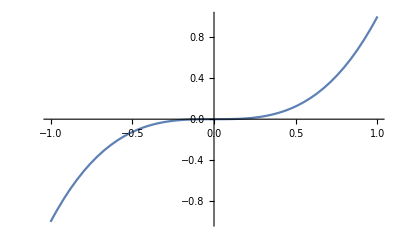

```mathematica
Plot[x^3,{x,-1,1}]
```

```mathematica
Integrate [x^(a-1) (1-x)^(b-1) , {x,0,1}]
```

ConditionalExpression[(Gamma[a] Gamma[b])/Gamma[a+b],Re[a]>0&&Re[b]>0]

```mathematica
FullForm[%]
```

ConditionalExpression[Times[Gamma[a],Gamma[b],Power[Gamma[Plus[a,b]],-1]],And[Greater[Re[a],0],Greater[Re[b],0]]]

```mathematica
N[%46]
```

ConditionalExpression[(Gamma[a] Gamma[b])/Gamma[a+b],Re[a]>0.&&Re[b]>0.]

```mathematica
Sum[x^n/n! , {n,3,Infinity}]
```

1/2 (-2+2 ⅇ^x-2 x-x^2)

```mathematica
Product[ 1- 1/((2k)^2) , {k,1,10}]
```

44801898141/68719476736

```mathematica
N[44801898141/68719476736,10]
```

0.6519534238

```mathematica
RootApproximant[0.651953423817758448421955108642578125`10.]
```

Root[1-#1-#1^3-#1^8-#1^9-#1^10-#1^11+#1^12&,1]

```mathematica
Table[ a[i] , {i,1,4} ]
```

```mathematica
{a[1],a[2],a[3],a[4]}
```

```mathematica
Table[cx[k] , {k,-10,10}]
```

{cx[-10],cx[-9],cx[-8],cx[-7],cx[-6],cx[-5],cx[-4],cx[-3],cx[-2],cx[-1],cx[0],cx[1],cx[2],cx[3],cx[4],cx[5],cx[6],cx[7],cx[8],cx[9],cx[10]}

```mathematica
Table[ c[i,j ] , {i,1,2} , {j,1,5}]
```

{{c[1,1],c[1,2],c[1,3],c[1,4],c[1,5]},{c[2,1],c[2,2],c[2,3],c[2,4],c[2,5]}}

```mathematica
MatrixForm[{{c[1,1],c[1,2],c[1,3],c[1,4],c[1,5]},{c[2,1],c[2,2],c[2,3],c[2,4],c[2,5]}}]
```

(c[1,1] | c[1,2] | c[1,3] | c[1,4] | c[1,5]
c[2,1] | c[2,2] | c[2,3] | c[2,4] | c[2,5])

```mathematica
MatrixForm[Table[ c[i,j ] , {i,1,7} , {j,1,7}]]
```

(c[1,1] | c[1,2] | c[1,3] | c[1,4] | c[1,5] | c[1,6] | c[1,7]
c[2,1] | c[2,2] | c[2,3] | c[2,4] | c[2,5] | c[2,6] | c[2,7]
c[3,1] | c[3,2] | c[3,3] | c[3,4] | c[3,5] | c[3,6] | c[3,7]
c[4,1] | c[4,2] | c[4,3] | c[4,4] | c[4,5] | c[4,6] | c[4,7]
c[5,1] | c[5,2] | c[5,3] | c[5,4] | c[5,5] | c[5,6] | c[5,7]
c[6,1] | c[6,2] | c[6,3] | c[6,4] | c[6,5] | c[6,6] | c[6,7]
c[7,1] | c[7,2] | c[7,3] | c[7,4] | c[7,5] | c[7,6] | c[7,7])

```mathematica
Table[Print["i= ",i];tmp=i^2; tmp,{i,1,5}]
```

i= 1

i= 2

i= 3

i= 4

i= 5

{1,4,9,16,25}

```mathematica
M={{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

```mathematica
MatrixForm[M]
```

(a | b
c | d)

```mathematica
Table[a[i,j],{i,1,5},{j,1,5}]//MatrixForm
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4] | a[1,5]
a[2,1] | a[2,2] | a[2,3] | a[2,4] | a[2,5]
a[3,1] | a[3,2] | a[3,3] | a[3,4] | a[3,5]
a[4,1] | a[4,2] | a[4,3] | a[4,4] | a[4,5]
a[5,1] | a[5,2] | a[5,3] | a[5,4] | a[5,5])

```mathematica
M1={{l,g},{h,i}}//MatrixForm
```

(l | g
h | i)

```mathematica
M1.M
```

(l | g
h | i).(a | b
c | d)

```mathematica
Dot[M1,M]
```

(l | g
h | i).(a | b
c | d)

```mathematica
N[Dot[M1,M]]
```

(l | g
h | i).(a | b
c | d)

```mathematica
Det[M]
```

Det[(a | b
c | d)]

```mathematica
M
```

(a | b
c | d)

```mathematica
CharacteristicPolynomial[{{a,b},{c,d}},x]
```

-b c+a d-a x-d x+x^2

```mathematica
Eigenvalues[M]
```

Eigenvalues[(a | b
c | d)]

```mathematica
M3={{1,4},{5,6}}
```

{{1,4},{5,6}}

```mathematica
Det[M3]
```

-14

```mathematica
N[Det[M3]]
```

-14.

```mathematica
v=Eigenvectors[M3]
```

```mathematica
{{1/10 (-5+√105),1},{1/10 (-5-√105),1}}
W=Transpose[M3]
```

{{1/10 (-5+√105),1},{1/10 (-5-√105),1}}

{{1,5},{4,6}}

```mathematica
MatrixForm[W]
```

(1 | 5
4 | 6)

```mathematica
Inverse[W]//MatrixForm
```

(-3/7 | 5/14
2/7 | -1/14)

```mathematica
Inverse[W].M.W
```

{{-3/7,5/14},{2/7,-1/14}}.(a | b
c | d).{{1,5},{4,6}}

```mathematica
Mprova={{1,2}, {2,1}};
Mprova2={{1,3},{4,2}};
MatrixForm[Mprova.Mprova2]
MatrixForm[Mprova.Mprova2 - Mprova2.Mprova]
```

(9 | 7
6 | 8)

(2 | 2
-2 | -2)

```mathematica
sigma1={{0,1},{1,0}};
sigma2={{0,-I},{I,0}};
sigma3={{1,0},{0,-1}};

C12= (sigma1.sigma2 ) -( sigma2.sigma1);
  Print[" Il commutatore(12) tra [ " , MatrixForm[sigma1] , "  ,  " , MatrixForm[sigma2] ,"  ] = " , MatrixForm[C12] , "      Dalla teoria infatti = " , 2 I  MatrixForm[sigma3 ]," = ", MatrixForm[C12] ,  "         (      2 " , I , " (sigma3)    ) "];

Print[  ];
Print[  ];
Print[  ];

C13= (sigma1.sigma3 - sigma3.sigma1);
   Print[" Il commutatore(13) tra [ " , MatrixForm[sigma1] , "  ,  " , MatrixForm[sigma3] ,"  ] = " ,MatrixForm[ C13 ] , "      Dalla teoria infatti = " , 2 I  MatrixForm[sigma2 ]," = ", MatrixForm[C13] ,  "         (      2 " , I , " (sigma2)    ) "];

Print[  ];
Print[  ];
Print[  ];

C23=(sigma2.sigma3 - sigma3.sigma2);
   Print[" Il commutatore(23) tra [ " , MatrixForm[sigma2] , "  ,  " , MatrixForm[sigma3] ,"  ] = " , MatrixForm[C23 ], "      Dalla teoria infatti = " , 2 I  MatrixForm[sigma1 ], " = ", MatrixForm[C23] , "       (      2 " , I , " (sigma1)    ) "];
```

Il commutatore(12) tra [ (0 | 1
1 | 0)  ,  (0 | -ⅈ
ⅈ | 0)  ] = (2 ⅈ | 0
0 | -2 ⅈ)      Dalla teoria infatti = 2 ⅈ (1 | 0
0 | -1) = (2 ⅈ | 0
0 | -2 ⅈ)         (      2 ⅈ (sigma3)    )

Il commutatore(13) tra [ (0 | 1
1 | 0)  ,  (1 | 0
0 | -1)  ] = (0 | -2
2 | 0)      Dalla teoria infatti = 2 ⅈ (0 | -ⅈ
ⅈ | 0) = (0 | -2
2 | 0)         (      2 ⅈ (sigma2)    )

Il commutatore(23) tra [ (0 | -ⅈ
ⅈ | 0)  ,  (1 | 0
0 | -1)  ] = (0 | 2 ⅈ
2 ⅈ | 0)      Dalla teoria infatti = 2 ⅈ (0 | 1
1 | 0) = (0 | 2 ⅈ
2 ⅈ | 0)       (      2 ⅈ (sigma1)    )

```mathematica
Normal[Series[Sin[x],{x,0,5}]]
```

x-x^3/6+x^5/120

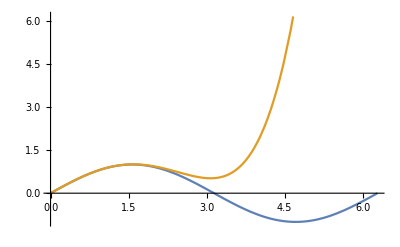

```mathematica
Plot[ {Sin[x], %1}, {x,0,2 Pi}]
```

```mathematica
??Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

Attributes[Sum]={HoldAll,Protected,ReadProtected}
 
Options[Sum]:={Assumptions:>$Assumptions,GenerateConditions→False,Method→Automatic,Regularization→None,VerifyConvergence→True}

```mathematica
Sum[x^n, {n,0,5}]
```

1+x+x^2+x^3+x^4+x^5

```mathematica
Sum[x^n, {n,0,Infinity}]
```

1/(1-x)

```mathematica
Sum[ n , {n,0,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=0)^∞ n

```mathematica
Sum[x^n/n! ,{n,3,Infinity}]
```

1/2 (-2+2 ⅇ^x-2 x-x^2)

```mathematica
Expand[%7]
```

-1+ⅇ^x-x-x^2/2

```mathematica
Sum[x^n/n! ,{n,0,Infinity}]
```

ⅇ^x

```mathematica
Table[a[i],{i,1,4}]
```

{a[1],a[2],a[3],a[4]}

```mathematica
Table[ Random[], {i,1,4}]
```

{0.829502,0.990021,0.907687,0.654479}

```mathematica
Table[pappo, {6}]
```

{pappo,pappo,pappo,pappo,pappo,pappo}

```mathematica
Plus @@%13
```

3.38169

```mathematica
Times @@%13
```

0.487858

```mathematica
Table[ a[i,j] , {i,1,4} , {j,1,2}]//MatrixForm
```

{{a[1,1],a[1,2]},{a[2,1],a[2,2]},{a[3,1],a[3,2]},{a[4,1],a[4,2]}}

```mathematica
%//MatrixForm
```

(a[1,1] | a[1,2]
a[2,1] | a[2,2]
a[3,1] | a[3,2]
a[4,1] | a[4,2])

```mathematica
lista=Table[ a[i,j] , {i,1,4} , {j,1,2}]
```

{{a[1,1],a[1,2]},{a[2,1],a[2,2]},{a[3,1],a[3,2]},{a[4,1],a[4,2]}}

```mathematica
lista[[3,2]]
```

a[3,2]

```mathematica
Table[            Print["i=",i];tmp=i^2;tmp,             {i,1,5}]    
(*l'elemento che viene inserito nella table è l'ultimo prima della virgola*)
```

i=1

i=2

i=3

i=4

i=5

{1,4,9,16,25}

```mathematica
lista1= Table[

     Print[" k = ",k];
    appo=k^2
     ,

{k,1,5}]
```

k = 1

k = 2

k = 3

k = 4

k = 5

{1,4,9,16,25}

```mathematica
Table[ a[i,j,k], {i,1,5} , {j,1,7} , {k,-1,9}]
```

{{{a[1,1,-1],a[1,1,0],a[1,1,1],a[1,1,2],a[1,1,3],a[1,1,4],a[1,1,5],a[1,1,6],a[1,1,7],a[1,1,8],a[1,1,9]},{a[1,2,-1],a[1,2,0],a[1,2,1],a[1,2,2],a[1,2,3],a[1,2,4],a[1,2,5],a[1,2,6],a[1,2,7],a[1,2,8],a[1,2,9]},{a[1,3,-1],a[1,3,0],a[1,3,1],a[1,3,2],a[1,3,3],a[1,3,4],a[1,3,5],a[1,3,6],a[1,3,7],a[1,3,8],a[1,3,9]},{a[1,4,-1],a[1,4,0],a[1,4,1],a[1,4,2],a[1,4,3],a[1,4,4],a[1,4,5],a[1,4,6],a[1,4,7],a[1,4,8],a[1,4,9]},{a[1,5,-1],a[1,5,0],a[1,5,1],a[1,5,2],a[1,5,3],a[1,5,4],a[1,5,5],a[1,5,6],a[1,5,7],a[1,5,8],a[1,5,9]},{a[1,6,-1],a[1,6,0],a[1,6,1],a[1,6,2],a[1,6,3],a[1,6,4],a[1,6,5],a[1,6,6],a[1,6,7],a[1,6,8],a[1,6,9]},{a[1,7,-1],a[1,7,0],a[1,7,1],a[1,7,2],a[1,7,3],a[1,7,4],a[1,7,5],a[1,7,6],a[1,7,7],a[1,7,8],a[1,7,9]}},{{a[2,1,-1],a[2,1,0],a[2,1,1],a[2,1,2],a[2,1,3],a[2,1,4],a[2,1,5],a[2,1,6],a[2,1,7],a[2,1,8],a[2,1,9]},{a[2,2,-1],a[2,2,0],a[2,2,1],a[2,2,2],a[2,2,3],a[2,2,4],a[2,2,5],a[2,2,6],a[2,2,7],a[2,2,8],a[2,2,9]},{a[2,3,-1],a[2,3,0],a[2,3,1],a[2,3,2],a[2,3,3],a[2,3,4],a[2,3,5],a[2,3,6],a[2,3,7],a[2,3,8],a[2,3,9]},{a[2,4,-1],a[2,4,0],a[2,4,1],a[2,4,2],a[2,4,3],a[2,4,4],a[2,4,5],a[2,4,6],a[2,4,7],a[2,4,8],a[2,4,9]},{a[2,5,-1],a[2,5,0],a[2,5,1],a[2,5,2],a[2,5,3],a[2,5,4],a[2,5,5],a[2,5,6],a[2,5,7],a[2,5,8],a[2,5,9]},{a[2,6,-1],a[2,6,0],a[2,6,1],a[2,6,2],a[2,6,3],a[2,6,4],a[2,6,5],a[2,6,6],a[2,6,7],a[2,6,8],a[2,6,9]},{a[2,7,-1],a[2,7,0],a[2,7,1],a[2,7,2],a[2,7,3],a[2,7,4],a[2,7,5],a[2,7,6],a[2,7,7],a[2,7,8],a[2,7,9]}},{{a[3,1,-1],a[3,1,0],a[3,1,1],a[3,1,2],a[3,1,3],a[3,1,4],a[3,1,5],a[3,1,6],a[3,1,7],a[3,1,8],a[3,1,9]},{a[3,2,-1],a[3,2,0],a[3,2,1],a[3,2,2],a[3,2,3],a[3,2,4],a[3,2,5],a[3,2,6],a[3,2,7],a[3,2,8],a[3,2,9]},{a[3,3,-1],a[3,3,0],a[3,3,1],a[3,3,2],a[3,3,3],a[3,3,4],a[3,3,5],a[3,3,6],a[3,3,7],a[3,3,8],a[3,3,9]},{a[3,4,-1],a[3,4,0],a[3,4,1],a[3,4,2],a[3,4,3],a[3,4,4],a[3,4,5],a[3,4,6],a[3,4,7],a[3,4,8],a[3,4,9]},{a[3,5,-1],a[3,5,0],a[3,5,1],a[3,5,2],a[3,5,3],a[3,5,4],a[3,5,5],a[3,5,6],a[3,5,7],a[3,5,8],a[3,5,9]},{a[3,6,-1],a[3,6,0],a[3,6,1],a[3,6,2],a[3,6,3],a[3,6,4],a[3,6,5],a[3,6,6],a[3,6,7],a[3,6,8],a[3,6,9]},{a[3,7,-1],a[3,7,0],a[3,7,1],a[3,7,2],a[3,7,3],a[3,7,4],a[3,7,5],a[3,7,6],a[3,7,7],a[3,7,8],a[3,7,9]}},{{a[4,1,-1],a[4,1,0],a[4,1,1],a[4,1,2],a[4,1,3],a[4,1,4],a[4,1,5],a[4,1,6],a[4,1,7],a[4,1,8],a[4,1,9]},{a[4,2,-1],a[4,2,0],a[4,2,1],a[4,2,2],a[4,2,3],a[4,2,4],a[4,2,5],a[4,2,6],a[4,2,7],a[4,2,8],a[4,2,9]},{a[4,3,-1],a[4,3,0],a[4,3,1],a[4,3,2],a[4,3,3],a[4,3,4],a[4,3,5],a[4,3,6],a[4,3,7],a[4,3,8],a[4,3,9]},{a[4,4,-1],a[4,4,0],a[4,4,1],a[4,4,2],a[4,4,3],a[4,4,4],a[4,4,5],a[4,4,6],a[4,4,7],a[4,4,8],a[4,4,9]},{a[4,5,-1],a[4,5,0],a[4,5,1],a[4,5,2],a[4,5,3],a[4,5,4],a[4,5,5],a[4,5,6],a[4,5,7],a[4,5,8],a[4,5,9]},{a[4,6,-1],a[4,6,0],a[4,6,1],a[4,6,2],a[4,6,3],a[4,6,4],a[4,6,5],a[4,6,6],a[4,6,7],a[4,6,8],a[4,6,9]},{a[4,7,-1],a[4,7,0],a[4,7,1],a[4,7,2],a[4,7,3],a[4,7,4],a[4,7,5],a[4,7,6],a[4,7,7],a[4,7,8],a[4,7,9]}},{{a[5,1,-1],a[5,1,0],a[5,1,1],a[5,1,2],a[5,1,3],a[5,1,4],a[5,1,5],a[5,1,6],a[5,1,7],a[5,1,8],a[5,1,9]},{a[5,2,-1],a[5,2,0],a[5,2,1],a[5,2,2],a[5,2,3],a[5,2,4],a[5,2,5],a[5,2,6],a[5,2,7],a[5,2,8],a[5,2,9]},{a[5,3,-1],a[5,3,0],a[5,3,1],a[5,3,2],a[5,3,3],a[5,3,4],a[5,3,5],a[5,3,6],a[5,3,7],a[5,3,8],a[5,3,9]},{a[5,4,-1],a[5,4,0],a[5,4,1],a[5,4,2],a[5,4,3],a[5,4,4],a[5,4,5],a[5,4,6],a[5,4,7],a[5,4,8],a[5,4,9]},{a[5,5,-1],a[5,5,0],a[5,5,1],a[5,5,2],a[5,5,3],a[5,5,4],a[5,5,5],a[5,5,6],a[5,5,7],a[5,5,8],a[5,5,9]},{a[5,6,-1],a[5,6,0],a[5,6,1],a[5,6,2],a[5,6,3],a[5,6,4],a[5,6,5],a[5,6,6],a[5,6,7],a[5,6,8],a[5,6,9]},{a[5,7,-1],a[5,7,0],a[5,7,1],a[5,7,2],a[5,7,3],a[5,7,4],a[5,7,5],a[5,7,6],a[5,7,7],a[5,7,8],a[5,7,9]}}}

```mathematica
Dimensions[%34]
```

{5,7,11}

```mathematica
Times@@{5,7,11}
```

385

```mathematica
M = { {a,b} ,{c,d} }
```

{{a,b},{c,d}}

```mathematica
MatrixForm[M]
```

(a | b
c | d)

```mathematica
Transpose[M]
```

{{a,c},{b,d}}

```mathematica
Transpose[M]//MatrixForm
```

(a | c
b | d)

```mathematica
Det[M]
```

-b c+a d

```mathematica
Eigenvalues[M]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
Eigenvectors[M]
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}

```mathematica
Inverse[M]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

```mathematica
MatrixForm[%]
```

(d/(-b c+a d) | -b/(-b c+a d)
-c/(-b c+a d) | a/(-b c+a d))

```mathematica
inversa=Inverse[M]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

```mathematica
inversa.M
```

{{-(b c)/(-b c+a d)+(a d)/(-b c+a d),0},{0,-(b c)/(-b c+a d)+(a d)/(-b c+a d)}}

```mathematica
Simplify[%]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
x1= Table[ x[i] , {i,1,4}]
```

{x[1],x[2],x[3],x[4]}

```mathematica
y1= Table[ y[i] , {i,1,4}]
```

{y[1],y[2],y[3],y[4]}

```mathematica
x1.y1      //riga *colonna
```

x[1] y[1]+x[2] y[2]+x[3] y[3]+x[4] y[4]

```mathematica
x1 y1     //prodotto ordinario
```

{x[1] y[1],x[2] y[2],x[3] y[3],x[4] y[4]}

```mathematica
M4=Table[ a[i,j] , {i,1,4} , {j,1,4}]
```

{{a[1,1],a[1,2],a[1,3],a[1,4]},{a[2,1],a[2,2],a[2,3],a[2,4]},{a[3,1],a[3,2],a[3,3],a[3,4]},{a[4,1],a[4,2],a[4,3],a[4,4]}}

```mathematica
M4.x1
```

{a[1,1] x[1]+a[1,2] x[2]+a[1,3] x[3]+a[1,4] x[4],a[2,1] x[1]+a[2,2] x[2]+a[2,3] x[3]+a[2,4] x[4],a[3,1] x[1]+a[3,2] x[2]+a[3,3] x[3]+a[3,4] x[4],a[4,1] x[1]+a[4,2] x[2]+a[4,3] x[3]+a[4,4] x[4]}

```mathematica
x1.M4
```

{a[1,1] x[1]+a[2,1] x[2]+a[3,1] x[3]+a[4,1] x[4],a[1,2] x[1]+a[2,2] x[2]+a[3,2] x[3]+a[4,2] x[4],a[1,3] x[1]+a[2,3] x[2]+a[3,3] x[3]+a[4,3] x[4],a[1,4] x[1]+a[2,4] x[2]+a[3,4] x[3]+a[4,4] x[4]}

```mathematica
sigma[1]={ {0,1} ,{1,0} };
sigma[2]={ {0,-I} ,{I,0} };
sigma[3]={ {1,0} ,{0,-1} };
commutatore[i_,j_ ] := sigma[i].sigma[j] - sigma[j].sigma[i];
rhs[i_,j_]:= 2  I  Sum[  Signature[ {i,j,k}] sigma[k] , {k,1,3} ];
	 test= Table[   commutatore[i,j] === rhs[i,j]    , {i,1,3} , {j,1,3}];
  test
```

{{True,True,True},{True,True,True},{True,True,True}}

```mathematica
M={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
inc={v1,v2}
```

{v1,v2}

```mathematica
Y1={0,0}
```

{0,0}

```mathematica
Y2={3,5}
```

{3,5}

```mathematica
M.inc//MatrixForm
```

(a v1+b v2
c v1+d v2)

```mathematica
Solve[M.inc==Y1,inc]
```

{{v1→0,v2→0}}

```mathematica
Solve[M.inc==Y2,inc]
```

{{v1→-(-5 b+3 d)/(b c-a d),v2→-(5 a-3 c)/(b c-a d)}}

```mathematica
(*Graffa più esterna soluzione del sistema (lineare, 1 soluzione, 1 elemento
Graffa più interna soluzione delle equazioni (2 equazioni, 2 elementi) *)
```

```mathematica
Clear[a,b,c];
Solve [ a x^2 + b x +c == 0 , x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
inc
```

{v1,v2}

```mathematica
soluzioni = inc/. %255
```

{{-(-5 b+3 d)/(b c-a d),-(5 a-3 c)/(b c-a d)}}

```mathematica
v1
```

v1

```mathematica
Solve [ {a v1 + b v2 ==3 , c v1 + d v2 == 5} , {v1,v2}]
```

{{v1→-(-5 b+3 d)/(b c-a d),v2→-(5 a-3 c)/(b c-a d)}}

```mathematica
//occhio alle graffe , simultaneamente tuttto quello tra graffe
```

```mathematica
eqs = {a v1 + b v2 ==7, c v1 + d v2 == 0};
```

```mathematica
inc = {v1,v2};
```

```mathematica
soluzioni3 = Solve[ eqs , inc];
```

```mathematica
soluzioni3
```

{{v1→(7 d)/(-b c+a d),v2→(7 c)/(b c-a d)}}

```mathematica
DSolve[ y''[x] + 4 y[x] == 0, y [x] , x]
```

{{y[x]→C[1] Cos[2 x]+C[2] Sin[2 x]}}

```mathematica
DSolve[{y''[x] + 4y[x] == 0 , y[0] ==0, y'[0]==1} , y[x] , x]
```

{{y[x]→1/2 Sin[2 x]}}

```mathematica
DSolve[{y''[x] + 4y[x] == 0 , y[0] ==1, y'[0]==0} , y[x] , x]
```

{{y[x]→Cos[2 x]}}

```mathematica
diff = %297
```

{{y[x]→C[1] Cos[2 x]+C[2] Sin[2 x]}}

```mathematica
D[diff,x]
```

{{y'[x]→2 C[2] Cos[2 x]-2 C[1] Sin[2 x]}}

```mathematica
diff /. x->0
```

{{y[0]→C[1]}}

```mathematica
NDSolve[ { y''[x]+4 y[x] ==0, y[0] ==0, y'[0] == 1 }, y[x], {x,0,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
sol[x_] = y[x] /. %
```

```mathematica
{InterpolatingFunction[…][x]}
```

```mathematica
Plot[sol[z], {z,0,6}]
```

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

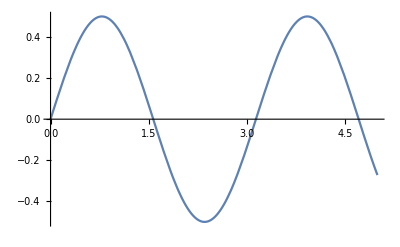

```mathematica
Plot[sol[z], {z,0,5}]
```